```mathematica
(* Physical parameters *)
Clear[P,L,DD,EE,nu]
(* Derived parameters *)
mu = EE/2/(nu+1);
lambda = EE nu / (1+nu)/(1-2 nu);
II = DD^3/12;

(* Closed form solutions *)
sxx=P x y/II;
syy=0;
sxy = P/2/II(DD^2/4-y^2);
u = -P/(2 EE II)(L^2-x^2)y -(P(2+nu))/(6 EE II)y^3 + (P(1+nu)DD^2)/(8 EE II)y//Simplify;
v =(-P L^3)/(6 EE II)(2-3 x/L (1-nu y^2/L^2) + x^3/L^3+3DD^2/4/L^2(1+nu)(1-x/L))//FullSimplify;
```

```mathematica
(* Total force is P *)
Integrate[sxy,{y,-DD/2,DD/2}]
```

P

```mathematica
(* Solves the eq. for plane stress *)
( (2 mu lambda)/(2 mu + lambda) + mu) Grad[Div[{u,v},{x,y}],{x,y}] + mu  Laplacian[{u,v},{x,y}]// Simplify
```

{0,0}

```mathematica
(* Check that stresses are correct *)
Div[{{sxx,sxy},{sxy,syy}},{x,y}] == {0, 0} // Simplify
eps = 1/2(Grad[{u,v},{x,y}] + Transpose@Grad[{u,v},{x,y}]) // Simplify;
sigma = (2 mu lambda)/(2 mu + lambda) Tr[eps] IdentityMatrix[2] + 2 mu eps //FullSimplify;
sigma == {{sxx,sxy},{sxy,syy}}//Simplify
```

True

True

```mathematica
(* Boundary conditions (remove semicolons to view) *)
u/.{x->L}//Simplify;
v/.{x->L}//Simplify;
u/.{x->0}//Simplify;
v/.{x->0}//Simplify;

u/.{y->-DD/2}//Simplify;
v/.{y->-DD/2}//Simplify;
u/.{y->DD/2}//Simplify;
v/.{y->DD/2}//Simplify;

sxx/.{x->0} // Simplify;
sxy/.{x->0} // Simplify;
```

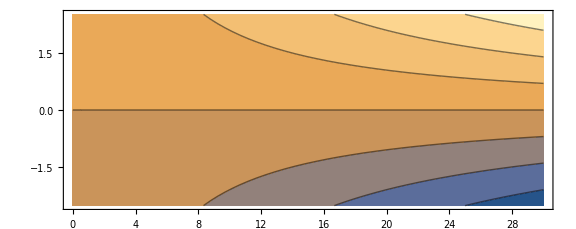
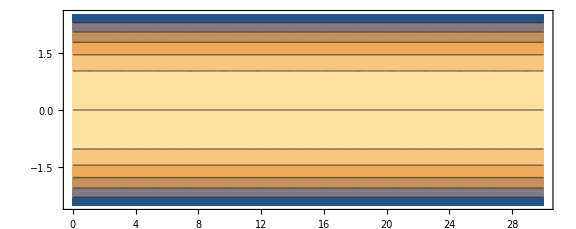
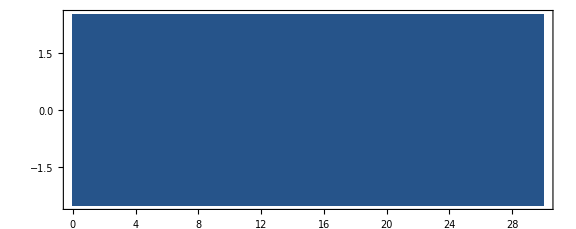

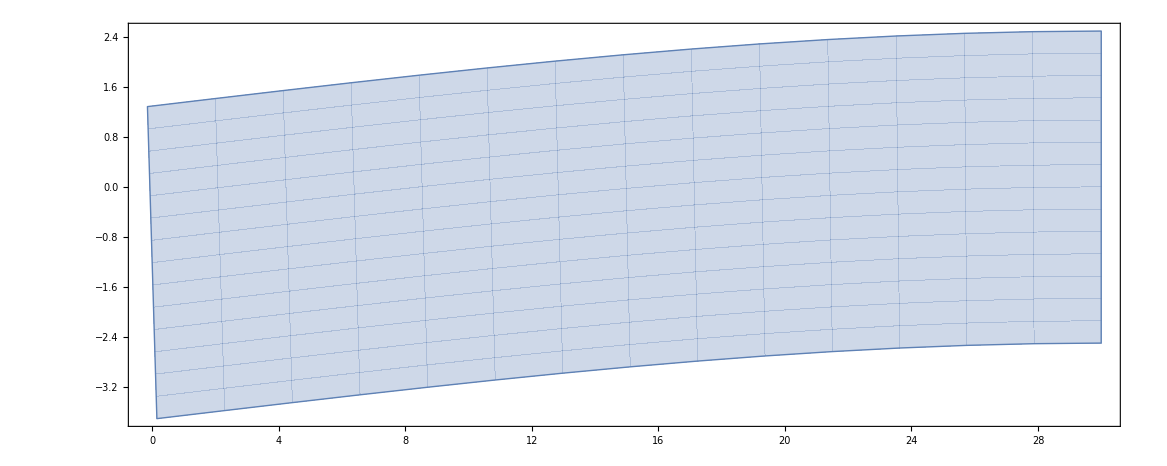

```mathematica
(* Numerical example *)
P = 1000;
L = 30;
DD = 5;
II=DD^3/12;
EE=72.1 10^9;
nu = 0.33;

(* Plots *)
{ContourPlot[sxx,{x,0,L},{y,-DD/2,DD/2}, AspectRatio->Automatic, ImageSize->Large],
ContourPlot[sxy,{x,0,L},{y,-DD/2,DD/2}, AspectRatio->Automatic, ImageSize->Large],
ContourPlot[syy,{x,0,L},{y,-DD/2,DD/2}, AspectRatio->Automatic, ImageSize->Large]}
f=10^5;
ParametricPlot[{x+f u,y+f v},{x,0,L},{y,-DD/2,DD/2}]
```